This Mathematica notebook contains the code used to simulate the model presented in “Fertilization by coral-dwelling fish promotes coral growth but can exacerbate bleaching response” by A.R. Detmer, R. Cunning, F. Pfab, A.L. Brown, A. C. Stier, R.M. Nisbet, and H.V. Moeller. It also contains the code to produce Figures 2, 4, 5, and 6 in the main text. Code for the supplementary figures is in “Fish Excretion Supplemental Figures.nb”.  

Note that external irradiance is denoted with an L in the following code; this is equivalent to  I in the main text

## Define constant parameters (run this first)

```mathematica
(* list of parameters and expressions that don't change, run this before running any of the other code*)
(*values that were varied in the model simulations are commented out here*)
(*parameters from original Cunning et al. 2017 model (see Table 2 of Cunning et al. 2017)*)
nNH=.18;(*N:C molar ratio in host biomass*)
nNS=.13; (*N:C molar ratio in symbiont biomass*)
nNX=.2; (*N:C molar ratio in prey biomass*)
j0HT=.03;(*maintenance rate of host biomass*)
j0ST=.03;(*maintenance rate of symbiont biomass*)
σNH=.9;(*proportion of N turnover recycled in host*)
σCH=.1;(*proportion host metabolic CO2 recycled to photosynthesis*)
σNS=.9;(*proportion of N turnover recycled in symbiont*)
σCS=.9;(*proportion symbiont metabolic CO2 recycled to photosynthesis*)
jXm=.13;(*maximum prey assimilation rate from host feeding*)
KX=10^-6;(*half-saturation constant for prey assimilation*)
jNm=.035; (*maximum host DIN uptake rate*)
KN=1.5*10^-6; (* half-saturation constant for host DIN uptake*)
kCO2=10; (*efficacy of CO2 delivery to photosynthesis by host carbon concentrating mechanisms*)
jHGm=1;(*maximum specific growth rate of host*)
yCL=.1; (*quantum yield of photosynthesis*)
yC=.8; (*yield of biomass formation from carbon*)
astar=1.34; (*effective light-absorbing cross-section of symbiont*)
kNPQ=112; (* non-photochemical quenching (NPQ) capacity of symbiont*)
kROS=80; (* excess photon energy that doubles ROS production relative to baseline levels *)
jCPm=2.8; (*maximum specific photosynthesis rate of symbiont*)
jSGm=0.25;(*maximum specific growth rate of symbiont*)
b=5;(*scaling parameter for bleaching response*)
(*X=0;*)(*concentration of prey in environment*)
(*Ν=1*10^-7;*)(* ambient concetration of nitrogen in external environment*)
L=15; (* external light*)
λ=50; (* Pfab et al. (submitted)'s lambda parameter for simulating fluxes as ODEs (continuous time approximation method for simulating the system) *)

(* parameters for host volume*)
kv=16.9; (* liters per C-mol H; calculated using using Edmunds & Burgess data on P. verrucosa, Mo'orea timeseries data on AFDW, and Schutter et al. 2010 estimate of host C content; see supplement for details*)
vi=0.7; (* fraction of coral volume occupied by water; based on Zawada et al. P. damicornis data; see supplement for details *)

(* parameters for fish*)
kp=210;(*scales fish carrying capacity with biomass of host, calculated using kv=16.9 C-mol/L*)
rp=0.05; (* intrinsic growth rate*)
Bp = 1; (* intraspecific competition coefficient*)
ep=1.5*10^-5; (* damselfish excretion rate (total mols N per g per d); calculated using data on D. flavicaudus; see supplement for details*)

(* parameters for nitrogen equations*)
α = 0.23; (* proportion of coral tissue in direct contact with the external environment; based on Zawada et al. 2019 P. damicornis data; see supplement for details *)

d=1660; (*flushing rate, units of 1/days; calculated using mean of the highest and lowest retention times from Holbrook et al. 2008; see supplement for details*)
ζ =1; (* fraction of waste N released by the symbiont that is bioavailable to the coral*)

(* derived parameters*)
(*jX=(jXm X)/(X+KX);*)(* prey uptake from environment*)
(* jN=(jNm Ν)/(Ν+KN);*) (* N uptake from environment*)
jHT=j0HT; (*rate of host biomass turnover*)
rNS=σNS nNS j0ST;(*nitrogen recycled from symbiont biomass turnover*)


(* initial conditions*)
H0=1; (*intial host biomass*)
S0=0.3; (*initial symbiont biomass*)
jCP0=1;
ρC0= 1; 
(*healthy state: jCP0 and ρC=jCPm or 1, bleached state: jCP0 and ρC=0 *)
VH0=kv*H0; (*initial host volume*)
(*Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)
(*jNw0= (jNm*Ν)/(Ν+KN)*H0/S0;*)
(*P0=0;*)(*kp*(1-α)*H0*)(*change P0 depending on whether or not fish are present*)


(*function to remove identifiers from simulations run in Module[]*)
str[expr_]:=Module[{},StringReplace[ToString[expr,FormatType->StandardForm],c:WordCharacter~~"$"~~DigitCharacter..:>c]];
```

## Model simulation

### Simulate the model

```mathematica
(* set environmental parameters: flushing rate and Nenv level*)
d=1660;(*flushing rate*)
Ν=1*10^-7;(* concentration of N in external env (Nenv in main text)*)

(*set level of prey and fish presence/absence: here, no prey or fish*)
X=0;(*concentration of prey in environment*)
P0=0(*kp*(1-α)*H0*); (*initial biomass of fish: either 0 if fish are absent or at initial carrying capacity=kp*(1-α)*H0 if fish are present*)
jX=(jXm X)/(X+KX);(*prey assimilation rate from host feeding*)
jN=(jNm Ν)/(Ν+KN); (*host uptake rate of nitrogen from external env (jNenv in main text)*)
Ni0 = Ν;(*initial concentration of nitrogen in interstitial space*)
jNi0 = (jNm Ν)/(Ν+KN);(*initial host uptake rate of nitrogen from interstitial space (jNi)*)

(*light function and its parameters*)
tStartStress=600; (*time at which light pulse starts*)
LHigh=0 ; (*magnitude of light pulse,note this is added to the constant light level L so the actual magnitude experienced by the system is L + LHigh*)
tHigh=0; (*duration of the light pulse*)
tmax=tStartStress+tHigh+100;(* length of simulation, here set to 100 days after the end of the light pulse*)

(*light function: step function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

(*function for the synthesizing units; same as 1/(1/ρ+1/A+1/B-1/(A+B)) so A and B are the two inputs (substrates) and ρ is the maximum production rate*)
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);

(* helper function for simulating host volume VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* fluxes that are calculated with algebraic equations: *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; (*host biomass formation rate*)
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];(*symbiont biomass formation rate*)
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];(*surplus nitrogen shared with the symbiont*)
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; (*excess carbon used to activate host CCMs*)
jCO2=jeC kCO2;(*CO2 input to photosynthesis*)
jL=A astar LfunH;(*light absorption rate *)
rCH=(jHT+(jHG (1-yC))/yC) σCH;(*recycled CO2 from host*)
rCS=σCS(j0ST+(1-yC)jSG yC^-1);(*recycled CO2 from symbiont*)
jeL=jL-jCP/yCL;(*light energy in excess of photochemistry*)
jNPQ=1/(1/jeL+1/kNPQ);(*total capacity of non-photochemical quenching of light energy*)
cROS1=(jeL-jNPQ)/kROS;(*ROS production proportional to baseline*)
jST=(1+b cROS1) j0ST;(*symbiont biomass turnover rate*)
rNH=σNH nNH jHT;(*recycled nitrogen from host turnover*)
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);(*light amplification factor*)

jNw= ρN*H/S+rNS-nNS*jSG; (*waste nitrogen released by symbiont*)

(*list of fluxes that are calculated with ODEs using Pfab et al.'s λ method*)
(*each sublist in tsolve has 3 components: the state variable, the equation for its exact (target) value, and the initial value*)
tsolve={
{ρC,jCP-jSG yC^-1,ρC0},(*surplus fixed carbon shared with the host*)
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},(*photosynthesis rate*)
{jNi, (jNm *Ni)/(Ni+KN), jNi0}(*host uptake rate of interstitial nitrogen*)
};

(*list of all the state variables: the first element of all the rows in tsolve plus H, S, VH, Ni, and P*)
states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
(* expression for changing all the state variables from X to X[t] instead of writing X[t] everywhere*)
addtimetostatevars=((#->#[t])&/@states); 

(* eqs= all the differential equations*)
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,(* flux X is described by the ODE X'=λ(X(...)-X) where X(...) is the equation for the exact value, Max is to make sure fluxes are never negative*)
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),(*specific growth of symbiont biomass*)
H'[t]==(H(jHG-jHT)/.addtimetostatevars),(*specific growth of host biomass*)
VH'[t]== fh[t, H'[t]],(*change in host colony volume*)
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
(* change in concentration of nitrogen in interstitial space*)
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) (*change in fish biomass*)
}
];
(*set initial conditions for the state variables*)
inis=Join[{
H[0]==H0,(*initial host biomass*)
S[0]==S0,(*initial symbiont biomass*)
VH[0]==VH0,(*initial host volume*)
Ni[0]== Ni0,(*initial interstitial nitrogen concentration*)
P[0]==P0},(*initial fish biomass*)
(#[[1]][0]==#[[3]])&/@tsolve];(* for each state variable in tsolve the initial value is equal to the third element of the sublist corresponding to that variable*)

(*simulate the model using the NDSolve function, eqs=equations, inis=initial conditions, #&/@states tells the function what the state variables are, simulate from time t=0 to tmax, name the output sol*)
sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

### Plot time series from this simulation

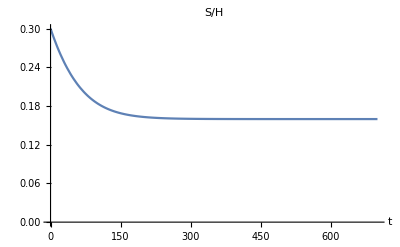
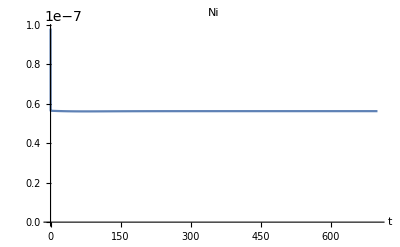
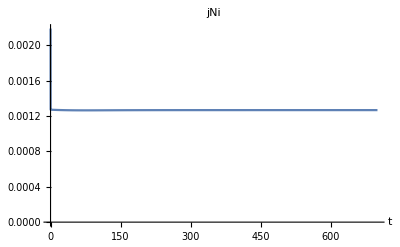
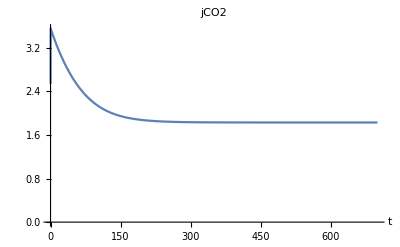
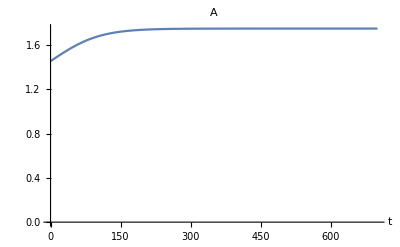
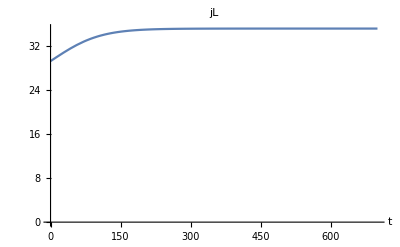
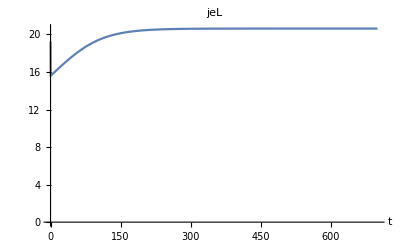
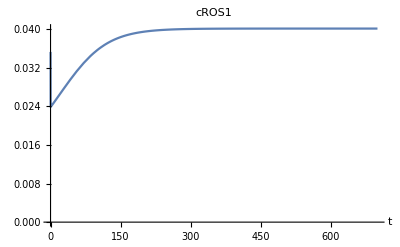

```mathematica
(* list of names for labeling the plots of the fluxes*)
names={jHG->"jHG",ρN->"ρN",jeC->"jeC",jCO2->"jCO2",jL->"jL",rCH->"rCH",rCS->"rCS",jCP->"jCP",jeL->"jeL",jNPQ->"jNPQ",cROS1->"cROS1",jSG->"jSG",ρC->"ρC",jST->"jST",A->"A",Log[Min[jCPm,rCS+(H (jCO2+rCH))/S]/Min[jCPm,jL yCL]]->"PS SU Lim",Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]->"S SU Lim",Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]->"H SU Lim",S/H->"S/H", Ni-> "Ni", jNi-> "jNi"};
(* list of fluxes and state variables to plot*)
toplot={S/H,Ni,jNi,jCO2,A,jL,jeL,cROS1,jCP,jNPQ,jST,jSG,rCS,jHG,rCH,ρC,jeC,ρN,Log[Min[jCPm,rCS+(H (jCO2+rCH))/S]/Min[jCPm,jL yCL]](*C-/L-limitation of photsynthesis SU*),Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]](*C-/N-limitation of symbiont biomass SU*),Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]](*C-/N-limitation of host biomass SU*)};

(*plot all the fluxes*)
(* Table[] is saying that for each element x in toplot, plot the results of the simulations of this variable*)
Table[Plot[{Evaluate@Flatten@{x/.addtimetostatevars/.sol}},{t,0, tmax}(* plot from time=0 to tmax *),PlotLabel->(x/.names),AxesLabel->{"t"},PlotRange->Full,AxesOrigin->{0,0}],{x,toplot}]

(*plot host and symbiont specific growth rates*)
Multicolumn[{Plot[{Evaluate[{H'[t]/H[t]}/.sol]},{t,0, tmax},PlotLabel->"dH/Hdt",PlotRange->Full,AxesLabel->{"t"},ImageSize->Medium,AxesOrigin->{0,0}],
Plot[{Evaluate[{S'[t]/S[t]}/.sol]},{t,0, tmax},PlotLabel->"dS/Sdt",PlotRange->Full,AxesLabel->{"t"},ImageSize->Medium,AxesOrigin->{0,0}]}, 2]
```

## Code to produce Figure 2 (Bifurcation diagrams)

### Simulations varying flushing rate

#### Check that steady state is reached

The system was considered to have reached the steady state when the percent change in the state variables over the last 50 days of the simulation was less than 0.001%.

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

jN=(jNm Ν)/(Ν+KN); (*rate of N uptake from external environment (Subscript[N, env] in text)*)
Ni0 = Ν; (*initial concentration of N in interstitial space*)
jNi0 = (jNm Ν)/(Ν+KN);(*initial rate of N uptake from interstitial space*)

tmax=800; (*max length of simulation*)

dBifurRuns1=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B)) , equation for synthesizing units*)

(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*calculate change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*calculate change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(*calculate change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record change in steady state values over the last 50 days of each simulation*)],

{P0, {0, kp*(1-α)*H0}}],(*repeat this once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{d,{450,850,1250,1650,2050,2450,2850,3250,3650,4050}}(*repeat all this for different flushing rates;Holbrook et al. 2008 measurements ranged from 443 to 2880 (mean of 1660),this was in low flow environment,so here went from 450 to 4050 in intervals of 400*)
],
{X,{0, 1*10^-7}}(*repeat with and without prey*)
];
```

```mathematica
Select[Flatten[dBifurRuns1], #>1*10^-4&] (* check that none of the recorded values are greater than 10^-4=0.001%: this command should give no output*)
```

{}

#### Run the simulations

Repeat the above  but record the steady state values at the end of each simulation.

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flow and N level*)
d=1660;
Ν=1*10^-7;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 

dBifurRuns=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*record the steady state values from each simulation*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{d,{450,850,1250,1650,2050,2450,2850,3250,3650,4050}}(*repeat all this for different flushing rates*)
],
{X,{0, 1*10^-7}}(*repeat with and without prey*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["dBifur",dBifurRuns]
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["dBifur"];
```

#### Get the results in the correct form to plot

```mathematica
(*output is a nested list, innermost is all 3 recorded values for {P1, P2}, second level is flushing rate {d1, d2, ...d10},outer level is prey {X1,X2}, so have 2 groups of 10 groups of 2 groups with 3 recorded values each *)

(*getting the lists of values to plot (will have 4 (all fish/prey combinations) for each of the 3 outputs, so 12 lists total*)
dBifurNoX=dBifurRuns[[1]];(*just the simulations with no prey*)
(*transpose this to change the nested list from {{P1 at d1, P2 at d1}, {same for d2}, ...{same for d10}} to {{d1, d2, ... d10 at P1}, {same for P2}} *)
dseparatePNoX=Transpose[dBifurNoX];
(*no prey no fish*)
dBifurNoPNoX=dseparatePNoX[[1]];
(*group the recorded values (Ni, dH/Hdt, S/H)*)
separatedNoPNoX=Transpose[dBifurNoPNoX];
(*Ni values at each flushing rate for no fish no prey*)
dBifurNoPNoXNi=separatedNoPNoX[[1]];
(*dH/Hdt values at each flushing rate for no fish no prey*)
dBifurNoPNoXgrowth=separatedNoPNoX[[2]];
(*S/H values at each flushing rate for no fish no prey*)
dBifurNoPNoXSH=separatedNoPNoX[[3]];

(* no prey with fish*)
dBifurPNoX=dseparatePNoX[[2]];
(*group each output together*)
separatedPNoX=Transpose[dBifurPNoX];
(*Ni values at each flushing rate for no prey with fish*)
dBifurPNoXNi=separatedPNoX[[1]];
(*dH/Hdt values at each flushing rate for no prey with fish*)
dBifurPNoXgrowth=separatedPNoX[[2]];
(*S/H values at each flushing rate for no prey with fish*)
dBifurPNoXSH=separatedPNoX[[3]];

(*repeat the above for simulations with prey*)
(*simulations with prey*)
dBifurX=dBifurRuns[[2]];
dseparatePX=Transpose[dBifurX];
(*prey no fish*)
dBifurNoPX=dseparatePX[[1]];
separatedNoPX=Transpose[dBifurNoPX];
(*Ni values at each flushing rate for prey no fish*)
dBifurNoPXNi=separatedNoPX[[1]];
(*dH/Hdt values at each flushing rate for prey no fish*)
dBifurNoPXgrowth=separatedNoPX[[2]];
(*S/H values at each flushing rate for prey no fish*)
dBifurNoPXSH=separatedNoPX[[3]];

(* prey with fish*)
dBifurPX=dseparatePX[[2]];
separatedPX=Transpose[dBifurPX];
(*Ni values at each flushing rate for prey with fish*)
dBifurPXNi=separatedPX[[1]];
(*dH/Hdt values at each flushing rate for prey with fish*)
dBifurPXgrowth=separatedPX[[2]];
(*S/H values at each flushing rate for prey with fish*)
dBifurPXSH=separatedPX[[3]];

(*list of flushing rate values (the x-values for the plot)*)
dVals={450,850,1250,1650,2050,2450,2850,3250,3650,4050};

(*use Table to get the all the lists (each corresponding to a response variable at all the flushing rates for one of the four fish/prey combinations) in the correct form to plot*)
dBifurLists=Table[Module[{PlotList},PlotList=Transpose@{dVals,list}; PlotList], {list, {dBifurNoPNoXNi,dBifurPNoXNi,dBifurNoPXNi,dBifurPXNi,dBifurNoPNoXgrowth,dBifurPNoXgrowth,dBifurNoPXgrowth,dBifurPXgrowth,dBifurNoPNoXSH,dBifurPNoXSH,dBifurNoPXSH,dBifurPXSH}}];
(*1-4 of dBifurLists are the Ni values for 1. no P no X, 2. P no X, 3. no P X, and 4. P and X, 5-8 are the host growth values at these P/X combinations, and 9-12 are the S/H values*)

(*to add Nenv to the plots:*)
Ν=1*10^-7;
NenvVal={Ν,Ν,Ν,Ν,Ν,Ν,Ν,Ν,Ν,Ν};
dBifurNenvLine=Transpose@{dVals,NenvVal};
```

### Simulations varying Nenv

#### check if steady state is reached

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=1500; 

N2BifurRuns1=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(* change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the changes as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{Ν,{0.1*10^-7,0.5*10^-7,1*10^-7, 2*10^-7, 3*10^-7,4*10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10*10^-7}}(*repeat all this for different values of Nenv*)
],

{X,{0, 1*10^-7}}(*with and without prey*)
];
```

```mathematica
Select[Flatten[N2BifurRuns1], #>1*10^-4&] (* check whether any of the recorded values are greater than 10^-4=0.001%*)
Position[N2BifurRuns1,_?(#>1*10^-4&)](* check for which of the parameter combinations the system did not reach the steady state: first level is 1=no prey, 2=prey, second level is Nenv (1=0.1*10^-7, etc.),3rd level is 1=no fish, 2=fish,4th level is the recorded value (1=Ni, 2=host growth, 3=S/H)*)(*so when there is no prey and Nenv is at the first and second lowest values tested and there are no fish, the change in both Ni and host growth greater than 10^-4 *)
```

{0.000826753,0.000233035,0.002002,0.0439383}

{{1,1,1,1},{1,1,1,2},{1,2,1,1},{1,2,1,2}}

The system has reached the steady state by 1500 time steps in all cases except the no fish, no prey cases when Nenv=1*10^-8 or 5*10^-8.  In these cases, host growth rate and interstitial nitrogen are still changing, and the simulation needs to be run for more time steps before the change in host growth rate  and interstitial N meet the steady state criteria. 

Re-run the simulation with no fish, no prey,  and Nenv=1*10^-8 with tmax=2500:

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-8 ;

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=2500; 

N2BifurRuns2Test=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(* change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the changes as output*)];
```

```mathematica
Select[Flatten[N2BifurRuns2Test], #>1*10^-4&]
```

{}

Re-run the simulation with no fish, no prey,  and Nenv=5*10^-8 with tmax=50,000:

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=5*10^-8 ;

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=50000; 

N2BifurRuns3Test=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},


F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=If[Chop[Evaluate[H'[tmax]/H[tmax]/.sol]]==0 && Chop[Evaluate[H'[tmax-50]/H[tmax-50]/.sol]]==0, 0,Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]] ];(*Chop[] approximates numbers that are less than 10^-10 as 0, so in this case, if host growth rate is less than 10^-10 at the end of the time step (asymptotically approaching 0), say that the percent change is equal to zero*)

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the changes as output*)];
```

```mathematica
Select[Flatten[N2BifurRuns3Test], #>1*10^-4&]
```

{}

#### Run the simulations

Run all simulations to tmax=1500 (sufficient to reach steady state in all scenarios except the no fish, no prey case when Nenv=1*10^-8 and Nenv=5*10^-8, which are re-run separately below.

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=1500; 

N2BifurRuns=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*record the steady state values as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{Ν,{0.1*10^-7,0.5*10^-7,1*10^-7, 2*10^-7, 3*10^-7,4*10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10*10^-7}}(*repeat all this for different values of Nenv*)
],

{X,{0, 1*10^-7}}(*with and without prey*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["NBifur",N2BifurRuns]
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["NBifur"];
```

Run simulations for the Nenv=1*10^-8 case.

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-8 ;

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=2500; 

N2BifurRuns2=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];
```

Run simulations for the Nenv=5*10^-8 case

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=5*10^-8 ;

X=0;
P0=0;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=5*10^6; 

N2BifurRuns3=
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Chop[Evaluate[H'[tmax]/H[tmax]/.sol]];(*since dH/Hdt is asymptotically approaching zero, set it to zero if it is less than 10^-10*)

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];
{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (will have 4 (all fish/prey combinations) for each of the 3 outputs, so 12 lists total*)
N2BifurNoX=N2BifurRuns[[1]];(*just the simulations with no prey*)
(*transpose this to change the nested list from {{P1 at N1, P2 at N1}, {N2}, ...{Nn}} to {{N1, N2, ... Nn at P1}, {P2}} *)
N2separatePNoX=Transpose[N2BifurNoX];
(*no prey no fish*)
N2BifurNoPNoX=N2separatePNoX[[1]];
separateN2NoPNoX=Transpose[N2BifurNoPNoX];(*group each output together*)
(*Ni values at each N for no fish no prey*)
N2BifurNoPNoXNi=Flatten[{N2BifurRuns2[[1]],N2BifurRuns3[[1]],separateN2NoPNoX[[1]][[3;;12]]}];
(*dH/Hdt values at each N for no fish no prey*)
N2BifurNoPNoXgrowth=Flatten[{N2BifurRuns2[[2]],N2BifurRuns3[[2]],separateN2NoPNoX[[2]][[3;;12]]}];
(*S/H values at each N for no fish no prey*)
N2BifurNoPNoXSH=Flatten[{N2BifurRuns2[[3]],N2BifurRuns3[[3]],separateN2NoPNoX[[3]][[3;;12]]}];

(* no prey with fish*)
N2BifurPNoX=N2separatePNoX[[2]];
separateN2PNoX=Transpose[N2BifurPNoX];(*group each output together*)
(*Ni values at each N for with fish no prey*)
N2BifurPNoXNi=separateN2PNoX[[1]];
(*dH/Hdt values at each N for with fish no prey*)
N2BifurPNoXgrowth=separateN2PNoX[[2]];
(*S/H values at each N for with fish no prey*)
N2BifurPNoXSH=separateN2PNoX[[3]];

N2BifurX=N2BifurRuns[[2]];(*simulations with prey*)
(*transpose this to change the nested list from {{P1 at N1, P2 at N1}, {N2}, ...{Nn}} to {{N1, N2, ... Nn at P1}, {P2}} *)
N2separatePX=Transpose[N2BifurX];
(*prey no fish*)
N2BifurNoPX=N2separatePX[[1]];
separateN2NoPX=Transpose[N2BifurNoPX];(*group each output together*)
(*Ni values at each N for no fish with prey*)
N2BifurNoPXNi=separateN2NoPX[[1]];
(*dH/Hdt values at each N for no fish with prey*)
N2BifurNoPXgrowth=separateN2NoPX[[2]];
(*S/H values at each N for no fish with prey*)
N2BifurNoPXSH=separateN2NoPX[[3]];
(* prey with fish*)
N2BifurPX=N2separatePX[[2]];
separateN2PX=Transpose[N2BifurPX];(*group each output together*)
(*Ni values at each N with fish and prey*)
N2BifurPXNi=separateN2PX[[1]];
(*dH/Hdt values at each N for with fish and prey*)
N2BifurPXgrowth=separateN2PX[[2]];
(*S/H values at each N for with fish and prey*)
N2BifurPXSH=separateN2PX[[3]];

(*list of flushing rate values*)
N2Vals={0.1*10^-7,0.5*10^-7,1*10^-7, 2*10^-7, 3*10^-7,4*10^-7,5*10^-7,6*10^-7,7*10^-7,8*10^-7,9*10^-7,10*10^-7};
N2BifurNenvLine=Transpose@{N2Vals,N2Vals};(*1:1 line for Ni and Nenv*)

(*use Table to get the lists in the form to plot*)
N2BifurLists=Table[Module[{PlotList},PlotList=Transpose@{N2Vals,list}; PlotList], {list, {N2BifurNoPNoXNi,N2BifurPNoXNi,N2BifurNoPXNi,N2BifurPXNi,N2BifurNoPNoXgrowth,N2BifurPNoXgrowth,N2BifurNoPXgrowth,N2BifurPXgrowth,N2BifurNoPNoXSH,N2BifurPNoXSH,N2BifurNoPXSH,N2BifurPXSH}}];
(*1-4 of N2BifurLists are the Ni values for 1. no P no X, 2. P no X, 3. no P X, and 4. P and X, 5-8 are the host growth values at these P/X combinations, and 9-12 are the S/H values*)
```

### Simulations varying fish carrying capacity

#### check if steady state is reached

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 

kpBifurRuns1=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P01*kp*(1-α)*H0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(* change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(*change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];

{steadyNi,steadyHGrowth,steadySH}(*record the changes as output*)],

{P01, {0, 1}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0) but since kp is changing, use a dummy variable P01 in order to have kp only change within Table and not also in the values to iterate over*)
{kp,{150,175,200,225,250,275,300,325,350,375,400}}(*repeat all this for different values of the scalar relating host biomass to fish carrying capacity*)
],
{X,{0, 1*10^-7}}(*with and without prey*)
];
```

```mathematica
Select[Flatten[kpBifurRuns1], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 

kpBifurRuns=Table[
Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P01*kp*(1-α)*H0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*record the steady state values as output*)],

{P01, {0, 1}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0) but since kp is changing, use a dummy variable P01 in order to have kp only chnge within Table and not also in the values to iterate over*)
{kp,{150,175,200,225,250,275,300,325,350,375,400}}(*repeat all this for different kp's*)
],
{X,{0, 1*10^-7}}(*with and without prey*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["kpBifur",kpBifurRuns]
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["kpBifur"];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (will have 4 (all fish/prey combinations) for each of the 3 outputs, so 12 lists total*)
kpBifurNoX=kpBifurRuns[[1]];(*just the simulations with no prey*)
(*transpose this to change the nested list from {{P1 at kp1, P2 at kp1}, {kp2}, ...{kpn}} to {{kp1, kp2, ... kpn at P1}, {P2}} *)
kpseparatePNoX=Transpose[kpBifurNoX];
(*no prey no fish*)
kpBifurNoPNoX=kpseparatePNoX[[1]];
separatekpNoPNoX=Transpose[kpBifurNoPNoX];(*group each output together*)
(*Ni values at each kp for no fish no prey*)
kpBifurNoPNoXNi=separatekpNoPNoX[[1]];
(*dH/Hdt values at each kp for no fish no prey*)
kpBifurNoPNoXgrowth=separatekpNoPNoX[[2]];
(*S/H values at each kp for no fish no prey*)
kpBifurNoPNoXSH=separatekpNoPNoX[[3]];

(* no prey with fish*)
kpBifurPNoX=kpseparatePNoX[[2]];
separatekpPNoX=Transpose[kpBifurPNoX];(*group each output together*)
(*Ni values at each kp for with fish no prey*)
kpBifurPNoXNi=separatekpPNoX[[1]];
(*dH/Hdt values at each kp for with fish no prey*)
kpBifurPNoXgrowth=separatekpPNoX[[2]];
(*S/H values at each kp for with fish no prey*)
kpBifurPNoXSH=separatekpPNoX[[3]];

kpBifurX=kpBifurRuns[[2]];(*simulations with prey*)
(*transpose this to change the nested list from {{P1 at kp1, kp2 at kp1}, {kp2}, ...{kpn}} to {{kp1, kp2, ... kpn at P1}, {P2}} *)
kpseparatePX=Transpose[kpBifurX];
(*prey no fish*)
kpBifurNoPX=kpseparatePX[[1]];
separatekpNoPX=Transpose[kpBifurNoPX];(*group each output together*)
(*Ni values at each kp for no fish with prey*)
kpBifurNoPXNi=separatekpNoPX[[1]];
(*dH/Hdt values at each kp for no fish with prey*)
kpBifurNoPXgrowth=separatekpNoPX[[2]];
(*S/H values at each kp for no fish with prey*)
kpBifurNoPXSH=separatekpNoPX[[3]];

(* prey with fish*)
kpBifurPX=kpseparatePX[[2]];
separatekpPX=Transpose[kpBifurPX];(*group each output together*)
(*Ni values at each kp for with fish and prey*)
kpBifurPXNi=separatekpPX[[1]];
(*dH/Hdt values at each kp for with fish and prey*)
kpBifurPXgrowth=separatekpPX[[2]];
(*S/H values at each kp for with fish and prey*)
kpBifurPXSH=separatekpPX[[3]];

(*list of kp values*)
kpVals={150,175,200,225,250,275,300,325,350,375,400};
(*to add Nenv to the plots*)
Ν=1*10^-7;
kpNenvVal={Ν,Ν,Ν,Ν,Ν,Ν,Ν,Ν,Ν,Ν, Ν};
kpBifurNenvLine=Transpose@{kpVals,kpNenvVal};


(*use Table to get the lists in the form to plot*)
kpBifurLists=Table[Module[{PlotList},PlotList=Transpose@{kpVals,list}; PlotList], {list, {kpBifurNoPNoXNi,kpBifurPNoXNi,kpBifurNoPXNi,kpBifurPXNi,kpBifurNoPNoXgrowth,kpBifurPNoXgrowth,kpBifurNoPXgrowth,kpBifurPXgrowth,kpBifurNoPNoXSH,kpBifurPNoXSH,kpBifurNoPXSH,kpBifurPXSH}}];
(*1-4 of kpBifurLists are the Ni values for 1. no P no X, 2. P no X, 3. no P X, and 4. P and X, 5-8 are the host growth values at these P/X combinations, and 9-12 are the S/H values*)
```

### Simulations varying prey

#### check if steady state is reached

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 

X2BifurRuns1= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,maketmax, steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*change in Ni*)
steadyNi=Abs[(Evaluate[Ni[tmax]/.sol]-Evaluate[Ni[tmax-50]/.sol])/Evaluate[Ni[tmax-50]/.sol]];

(*change in host growth*)
steadyHGrowth=Abs[(Evaluate[H'[tmax]/H[tmax]/.sol]-Evaluate[H'[tmax-50]/H[tmax-50]/.sol])/Evaluate[H'[tmax-50]/H[tmax-50]/.sol]];

(* change in S/H*)
steadySH=Abs[(Evaluate[S[tmax]/H[tmax]/.sol]-Evaluate[S[tmax-50]/H[tmax-50]/.sol])/Evaluate[S[tmax-50]/H[tmax-50]/.sol]];


{steadyNi,steadyHGrowth,steadySH}(*record the changes as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7}}(*different levels of prey*)
];
```

```mathematica
Select[Flatten[X2BifurRuns1], #>1*10^-4&] (*nothing is greater than 10^-4*)
```

{}

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 ;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=800; 


X2BifurRuns= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,tsolve, addtimetostatevars,eqs,inis,sol,t,maketmax, steadyNi,steadyHGrowth,steadySH(*make sure to put any intermediate output values in Module*)},

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar L ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*steady state Ni*)
steadyNi=Evaluate[Ni[tmax]/.sol];

(*steady state host growth*)
steadyHGrowth=Evaluate[H'[tmax]/H[tmax]/.sol];

(*steady state S/H*)
steadySH=Evaluate[S[tmax]/H[tmax]/.sol];

{steadyNi,steadyHGrowth,steadySH}(*the steady state values as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7}}(*different levels of prey*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["XBifur",X2BifurRuns]
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["XBifur"];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (have 2 (fish/no fish) for each of the 3 outputs, so 6 lists total*)

(*transpose this to change the nested list from {{P1 at X1, P2 at X1}, {X2}, ...{Xn}} to {{X1, X2, ... Xn at P1}, {P2}} *)
XseparatePX=Transpose[X2BifurRuns];
(*prey no fish*)
XBifurNoPX=XseparatePX[[1]];
separateXNoPX=Transpose[XBifurNoPX];(*group each output together*)
(*Ni values at each X for no fish*)
XBifurNoPXNi=separateXNoPX[[1]];
(*dH/Hdt values at each X for no fish*)
XBifurNoPXgrowth=separateXNoPX[[2]];
(*S/H values at each X for no fish *)
XBifurNoPXSH=separateXNoPX[[3]];

(* prey with fish*)
XBifurPX=XseparatePX[[2]];
separateXPX=Transpose[XBifurPX];(*group each output together*)
(*Ni values at each X with fish*)
XBifurPXNi=separateXPX[[1]];
(*dH/Hdt values at each X with fish*)
XBifurPXgrowth=separateXPX[[2]];
(*S/H values at each X with fish*)
XBifurPXSH=separateXPX[[3]];


(*list of X values*)
XVals={0,0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7, 2*10^-7};
(*to add Nenv to the plots*)
Ν=1*10^-7;
XNenvVal=ConstantArray[Ν,Length[XVals]];
XBifurNenvLine=Transpose@{XVals,XNenvVal};

(*make list of the no prey values to plot as reference lines*)
noXnoPNiList=ConstantArray[XBifurNoPXNi[[1]],Length[XVals]];
noXPNiList=ConstantArray[XBifurPXNi[[1]],Length[XVals]];
noXnoPgrowthList=ConstantArray[XBifurNoPXgrowth[[1]],Length[XVals]];
noXPgrowthList=ConstantArray[XBifurPXgrowth[[1]],Length[XVals]];
noXnoPSHList=ConstantArray[XBifurNoPXSH[[1]],Length[XVals]];
noXPSHList=ConstantArray[XBifurPXSH[[1]],Length[XVals]];

(*use Table to get the lists in the form to plot*)
XBifurLists=Table[Module[{PlotList},PlotList=Transpose@{XVals,list}; PlotList], {list, {noXnoPNiList,noXPNiList,XBifurNoPXNi,XBifurPXNi,noXnoPgrowthList,noXPgrowthList,XBifurNoPXgrowth,XBifurPXgrowth,noXnoPSHList,noXPSHList,XBifurNoPXSH,XBifurPXSH}}];
```

### Make Figure 2

```mathematica
(*define padding for plots*)
padding={{80(*left*),22(*right*)}, {65(*bottom*),10 (*top*)}};

(*Ni vs Nenv*)
plota=ListLinePlot[{N2BifurLists[[1]], N2BifurLists[[2]],N2BifurLists[[3]], N2BifurLists[[4]],N2BifurNenvLine},Epilog->Text[Style["a)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->Full,PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[GrayLevel[0.73](*, Thin*)]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{{2*10^-7, "2*10^-7"},{6*10^-7, "6*10^-7"},{1*10^-6, "1*10^-6"}},None},{(*None*){{2*10^-7, "2*10^-7"},{6*10^-7, "6*10^-7"},{1*10^-6, "1*10^-6"}},None}},FrameLabel->{{"Interstitial N (mol L^-1)",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14(*12*)](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*dH/Hdt vs Nenv*)
plotb=ListLinePlot[{N2BifurLists[[5]], N2BifurLists[[6]],N2BifurLists[[7]], N2BifurLists[[8]]},Epilog->Text[Style["b)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->Full,PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0, 0.01,0.03,0.05},None},{(*None*){{2*10^-7, "2*10^-7"},{6*10^-7, "6*10^-7"},{1*10^-6, "1*10^-6"}},None}},FrameLabel->{{"Host specific growth rate \n (C-mol H C-mol H^-1 d^-1)",None}(*\n makes line break*),{"Ambient N (mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*Ni vs prey*)
plotc=ListLinePlot[{XBifurLists[[1]], XBifurLists[[2]],XBifurLists[[3]], XBifurLists[[4]],XBifurNenvLine},
Epilog->Text[Style["c)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->{Full,{0, 1.6*10^-7}}(*Full*),PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[GrayLevel[0.73](*, Thin*)]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{{4*10^-8, "4*10^-8"},{8*10^-8, "8*10^-8"},{1.2*10^-7, "1.2*10^-7"}},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},FrameLabel->{{None,None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*dH/Hdt vs prey*)
plotd=ListLinePlot[{XBifurLists[[5]], XBifurLists[[6]],XBifurLists[[7]], XBifurLists[[8]]},Epilog->Text[Style["d)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->{Full, {0, 0.026}},PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{0, 0.01,0.02},None},{(*None*){{0, "0"},{1*10^-7, "1*10^-7"},{2*10^-7, "2*10^-7"}},None}},FrameLabel->{{None,None},{"Prey (C-mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*Ni vs flushing rate*)
plote=ListLinePlot[{dBifurLists[[1]], dBifurLists[[2]],dBifurLists[[3]], dBifurLists[[4]],dBifurNenvLine},
Epilog->Text[Style["e)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->{Full,{0, 1.6*10^-7}}(*Full*),PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[GrayLevel[0.73](*, Thin*)]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{{4*10^-8, "4*10^-8"},{8*10^-8, "8*10^-8"},{1.2*10^-7, "1.2*10^-7"}},None},{(*None*){500, 1500,2500, 3500},None}},FrameLabel->{{None,None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*dH/Hdt vs flushing rate*)
plotf=ListLinePlot[{dBifurLists[[5]], dBifurLists[[6]],dBifurLists[[7]], dBifurLists[[8]]},Epilog->Text[Style["f)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->{Full, {0, 0.026}},PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->{{{0, 0.01,0.02},None},{(*None*){500, 1500,2500, 3500},None}},FrameLabel->{{None,None},{"Flushing rate (d^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*Ni vs kp*)
plotg=ListLinePlot[{kpBifurLists[[1]], kpBifurLists[[2]],kpBifurLists[[3]], kpBifurLists[[4]],kpBifurNenvLine},
Epilog->Text[Style["g)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->{Full,{0, 1.6*10^-7}},PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]],Directive[GrayLevel[0.73](*, Thin*)]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, FrameTicks->(*True*){{{{4*10^-8, "4*10^-8"},{8*10^-8, "8*10^-8"},{1.2*10^-7, "1.2*10^-7"}},None},{(*None*){150, 250, 350},None}},FrameLabel->{{None,None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*dH/Hdt vs kp*)
ploth=ListLinePlot[{kpBifurLists[[5]], kpBifurLists[[6]],kpBifurLists[[7]], kpBifurLists[[8]]},Epilog->Text[Style["h)",{Black,16}],Offset[{5(*right from top left*),-5(*down from top left*)},Scaled[{0,1}]],{-1,0}],LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],  ImagePadding->padding,PlotRange->{Full, {0, 0.026}},PlotStyle->{{ColorData[97,"ColorList"][[1]],Dashing[Large]}, {ColorData[97,"ColorList"][[2]],Dashing[Large]},ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, 
FrameTicks->{{{0, 0.01,0.02},None},{(*None*){150, 250, 350},None}},FrameLabel->{{None,None},{"Fish:host biomass scalar \n(g C-mol H^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,14](*axis label size*), AspectRatio->1.1(*1/GoldenRatio*)];

(*make the plot legend*)
BifurLeg=LineLegend[{ColorData[97,"ColorList"][[1]],{ColorData[97,"ColorList"][[1]],Dashing[Large]},  ColorData[97,"ColorList"][[2]],{ColorData[97,"ColorList"][[2]],Dashing[Large]}}, {"No fish, with prey","No fish, no prey","With fish, with prey","With fish, no prey"}, LegendLayout->{"Row",1}, LabelStyle->Directive[FontSize->14]]
```

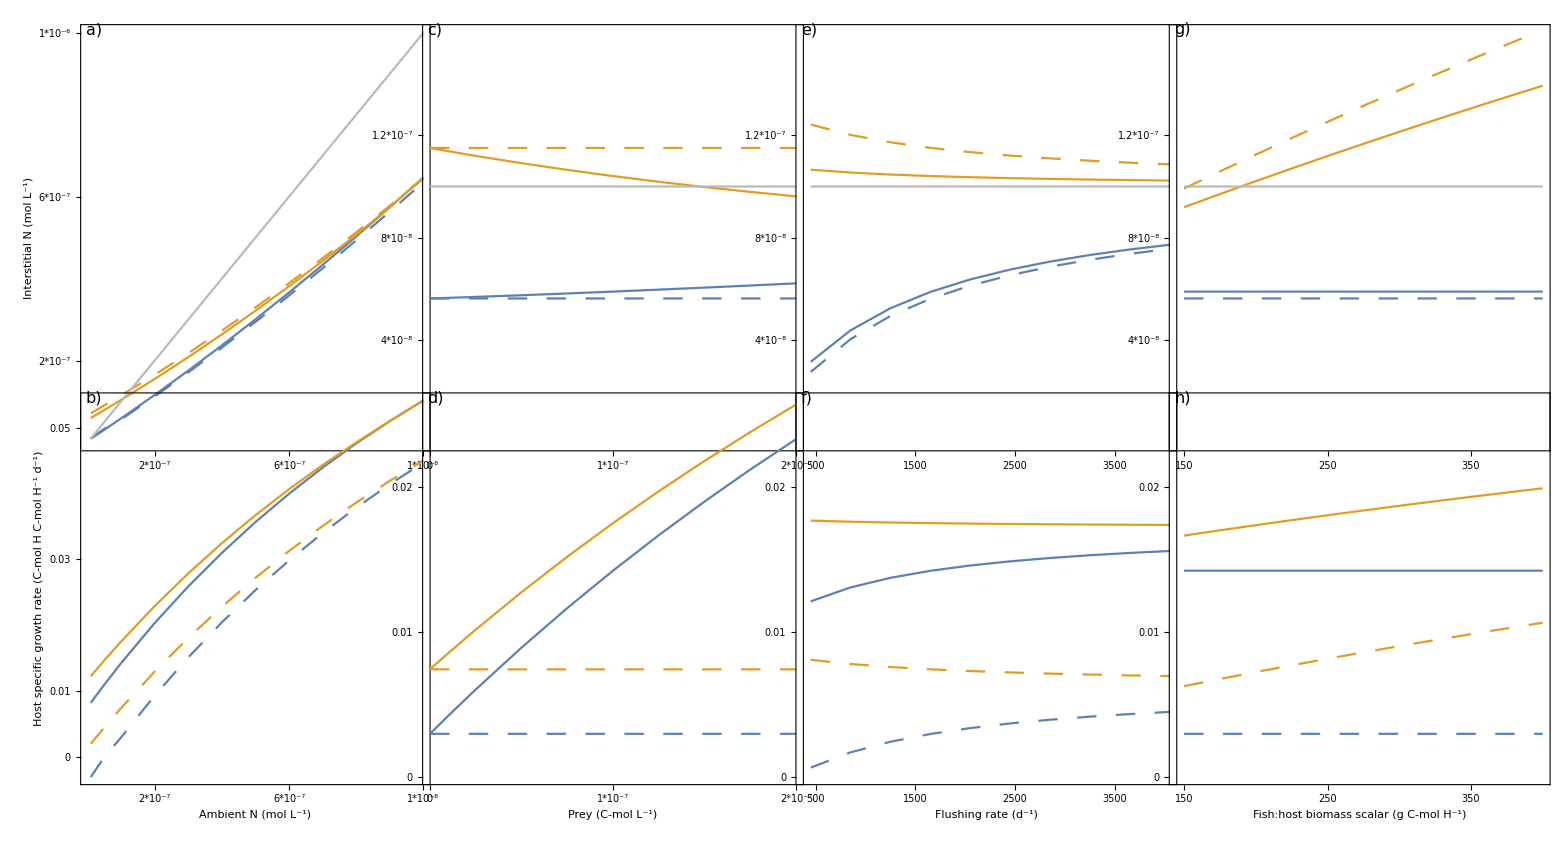

```mathematica
(*plot Figure 2*)
BifurFig=Show[Legended[GraphicsGrid[{{plota, plotc, plote, plotg},{plotb, plotd, plotf, ploth}}, ImageSize->Full,Spacings->{ {0(*left*),-60 (*labels and left col*),-60,-60(*left to right*)},{0(*top*),-100(*middle 2 rows*) (*labels and bottom*), 0(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom (*align the grid at the bottom of its frame*)],Placed[BifurLeg,(*Bottom*){Center(*left to right position is in the center*), 0(*top to bottom position*)}]], Graphics[Text["N_i=N_env",{260 (*more pos=farther right*),-110(*more neg=further down*)}]]]
```

```mathematica
(*export figure as pdf*)
Export["BifurFig.pdf",BifurFig,"PDF"]
```

BifurFig.pdf

## Code to produce Figure 4 (Time series with different levels of ambient N)

### Run simulations for the three Nenv levels

#### Low Nenv

```mathematica
(*clear parameters that are changing and intermediate values from simulations*)
ClearAll[Ν, X, P0,jX,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(*set level of prey and fish presence/absence: here, no prey or fish*)
X=0;
P0=0(*kp*(1-α)*H0*); 
jX=(jXm X)/(X+KX);(*prey assimilation rate from host feeding*)

(* set environment: flushing rate and Nenv level*)
d=1660;
Ν=1*10^-7;(* concentration of N in external env (Nenv), 1*10^-7 = low N*)

jN=(jNm Ν)/(Ν+KN);
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function and its parameters*)
tStartStress=600; (*time at which light pulse starts*)
LHigh=25 ; (*magnitude of light pulse, NOTE: this is added to the constant light level L so the actual magnitude experienced by the system is L + LHigh*)
tHigh=30; (*duration of the light pulse*)
tmax=tStartStress+tHigh+100;(* length of simulation*)

(*light function: step function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*function for the synthesizing units; same as 1/(1/ρ+1/A+1/B-1/(A+B)) so A and B are the two inputs (substrates) and ρ is the maximum production rate*)

(* helper function for simulating host volume VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* fluxes that are calculated with algebraic equations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; (*host biomass formation rate*)
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];(*symbiont biomass formation rate*)
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];(*surplus nitrogen shared with the symbiont*)
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; (*excess carbon used to activate host CCMs*)
jCO2=jeC kCO2;(*CO2 input to photosynthesis*)
jL=A astar LfunH;(*light absorption rate; changed L to Lfun9 for light pulse *)
rCH=(jHT+(jHG (1-yC))/yC) σCH;(*recycled CO2 from host*)
rCS=σCS(j0ST+(1-yC)jSG yC^-1);(*recycled CO2 from symbiont*)
jeL=jL-jCP/yCL;(*light energy in excess of photochemistry*)
jNPQ=1/(1/jeL+1/kNPQ);(*total capacity of non-photochemical quenching of light energy*)
cROS1=(jeL-jNPQ)/kROS;(*ROS production proportional to baseline*)
jST=(1+b cROS1) j0ST;(*symbiont biomass turnover rate*)
rNH=σNH nNH jHT;(*recycled nitrogen from host turnover*)
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);(*light amplification factor*)

jNw= ρN*H/S+rNS-nNS*jSG; (*waste nitrogen released by symbiont*)

(*list of fluxes that are calculated with ODEs using Ferdi's λ method*)
tsolve={
{ρC,jCP-jSG yC^-1,ρC0},(*surplus fixed carbon shared with the host*)
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},(*photosynthesis rate*)
{jNi, (jNm *Ni)/(Ni+KN), jNi0}(*host uptake rate of interstitial nitrogen*)
};

(*list of all the state variables: the first element of all the rows in tsolve plus H, S, VH, Ni, and P*)
states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
(* expression for changing all the state variables from X to X[t] instead of writing X[t] everywhere*)
addtimetostatevars=((#->#[t])&/@states); 

(* eqs= all the differential equations*)
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,(* flux X is described by the ODE X'=λ(X(...)-X) where X(...) is the equation for the exact value, Max is to make sure fluxes are never negative*)
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),(*specific growth of symbiont biomass*)
H'[t]==(H(jHG-jHT)/.addtimetostatevars),(*specific growth of host biomass*)
VH'[t]== fh[t,H'[t]],(*change in host colony volume*)
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
(* change in concentration of nitrogen in interstitial space*)
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) (*change in fish biomass*)
}
];
(*set initial conditions for the state variables*)
inis=Join[{
H[0]==H0,(*initial host biomass*)
S[0]==S0,(*initial symbiont biomass*)
VH[0]==VH0,(*initial host volume*)
Ni[0]== Ni0,(*initial interstitial nitrogen concentration*)
P[0]==P0},(*initial fish biomass*)
(#[[1]][0]==#[[3]])&/@tsolve];(* for each state variable in tsolve the initial value is equal to the third element of the sublist corresponding to that variable*)

(*simulate the model using the NDSolve function, eqs=equations, inis=initial conditions, #&/@states tells the function what the state variables are, simulate from time t=0 to tmax, call the output solLowN*)
solLowN=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### Intermediate Nenv

```mathematica
(*clear parameters that are changing and intermediate values from simulations*)
ClearAll[Ν, X, P0,jX,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
X=0;
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-6;(*intermediate Nenv*)

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;
LHigh=25 ; 
tHigh=30;
tmax=tStartStress+tHigh+100; 

(*light functions*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);

jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

(*simulation for intermediate Nenv level*)
solMedN=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### High Nenv

```mathematica
(*clear parameters that are changing and intermediate values from simulations*)
ClearAll[Ν, X, P0,jX,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(*no prey or fish*)
X=0;
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-5;(*high Nenv*)

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tStartStress=600;
LHigh=25 ; 
tHigh=30;
tmax=tStartStress+tHigh+100; 

(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);

jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

(*simulation for high N levels*)
solHigherN=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
```

#### Saving the outputs from these simulations (optional)

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["lowN",solLowN]
Save["medN",solMedN]
Save["higherN",solHigherN]
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["lowN"];
Get["medN"];
Get["higherN"];
```

### Make Figure 4

```mathematica
(*colors: low Nenv=green, medium Nenv=blue and highest Nenv=yellow*)

(*define padding for plots*)
padding4={{50(*left*),15(*right*)}, {30(*bottom*),10 (*top*)}};

(*Fig. 4a host specific growth rate*)plot4a=Show[Plot[{Evaluate[{H'[t]/H[t]}/.solLowN],Evaluate[{H'[t]/H[t]}/.solMedN],Evaluate[{H'[t]/H[t]}/.solHigherN]},{t,590,640}(* plot starting 10 days before the light pulse to 10 days after it ends *),PlotLabel->"a) Host specific growth rate",ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]}(*colors for each N level: low N=green, medium N=blue and highest N=yellow*),Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"C-mol H C-mol H^-1 d^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09(*level*), 0.06(*opacity*)](*use RegionPlot[] to shade the region where the light pulse occurred*)]];

(*Fig. 4b nitrogen shared with symbiont*)plot4b=Show[Plot[{Evaluate@Flatten@{ρN/.addtimetostatevars/.solLowN},Evaluate@Flatten@{ρN/.addtimetostatevars/.solMedN},Evaluate@Flatten@{ρN/.addtimetostatevars/.solHigherN}},{t,590,640},PlotRange->Full,PlotLabel->"b) Nitrogen shared with symbiont (ρN)",ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"mol N C-mol H^-1 d^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(*Fig. 4c symbiont specific growth rate*)plot4c=Show[Plot[{Evaluate[{S'[t]/S[t]}/.solLowN],Evaluate[{S'[t]/S[t]}/.solMedN],Evaluate[{S'[t]/S[t]}/.solHigherN]},{t,590,640},PlotLabel->"c) Symbiont specific growth rate",ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"C-mol S C-mol S^-1 d^-1",None}(*\n makes line break*),{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

plot4d=Show[Plot[{Evaluate@Flatten@{S/H/.addtimetostatevars/.solLowN},Evaluate@Flatten@{S/H/.addtimetostatevars/.solMedN},Evaluate@Flatten@{S/H/.addtimetostatevars/.solHigherN}},{t,590,640},PlotLabel->"d) Symbiont to host biomass ratio",ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full,ImageSize->Full,AxesOrigin->{590,0}, PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"C-mol S C-mol H^-1",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(*Fig. 4e ROS production*)plot4e=Show[Plot[{Evaluate@Flatten@{cROS1/.addtimetostatevars/.solLowN},Evaluate@Flatten@{cROS1/.addtimetostatevars/.solMedN},Evaluate@Flatten@{cROS1/.addtimetostatevars/.solHigherN}},{t,590,640},PlotLabel->"e) ROS production (relative to baseline)",ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->Full, ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Relative",None},{None,None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];


(*Fig. 4h relative limitation of symbiont biomass synthesizing unit*)plot4h=Show[Plot[{Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.solLowN},Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.solMedN},Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.solHigherN}},{t,590,640},PlotRange->Full,PlotLabel->"h) Symbiont biomass C-/N-limitation",ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Relative",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(*Fig. 4g relative limitation of host biomass synthesizing unit*)plot4g=Show[Plot[{Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.solLowN},Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.solMedN},Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.solHigherN}},{t,590,640},PlotRange->Full,PlotLabel->"g) Host biomass C-/N-limitation", ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Relative",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];

(*carbon shared with host*)plot4f=Show[Plot[{Evaluate@Flatten@{ρC/.addtimetostatevars/.solLowN},Evaluate@Flatten@{ρC/.addtimetostatevars/.solMedN},Evaluate@Flatten@{ρC/.addtimetostatevars/.solHigherN}},{t,590,640},PlotRange->Full,PlotLabel->"f) Carbon shared with host (ρC)", ImagePadding->padding4,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImageSize->Full,AxesOrigin->{590,0},PlotStyle->{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]},Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"mol C C-mol S^-1 d^-1",None},{"Time (d)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)],RegionPlot[tStartStress<t<tStartStress+tHigh,{t,590,640},{y,-1000,1000}, Frame-> False, Mesh->None,BoundaryStyle->None, PlotStyle->GrayLevel[0.09, 0.06]]];
```

```mathematica
(*make the legend*)
NtsLeg=LineLegend[{ColorData[97,"ColorList"][[8]], ColorData[97,"ColorList"][[3]], ColorData[97,"ColorList"][[1]]}, {"Low N_env (10^-7 mol L^-1)","Med. N_env (10^-6 mol L^-1)","High N_env (10^-5 mol L^-1)"}, LegendMarkerSize->40(*, LegendLayout->{"Row",1}*)]
```

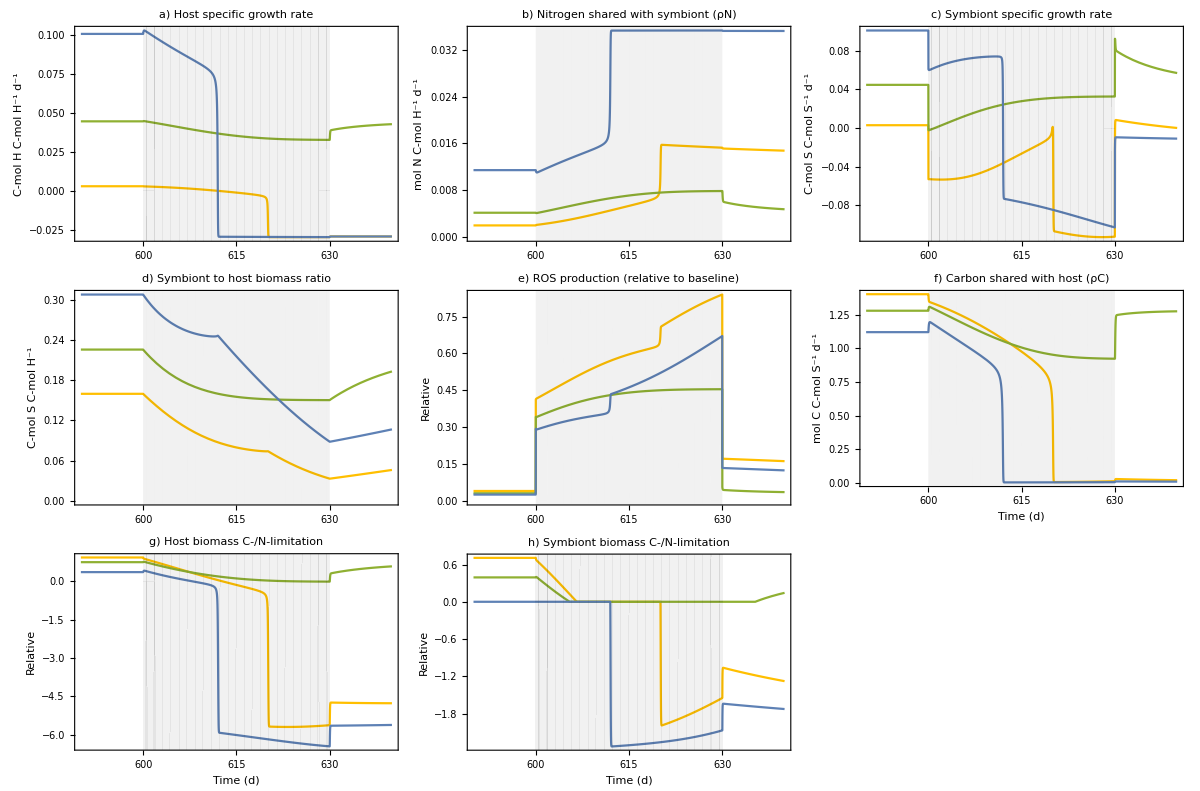

```mathematica
(*put everything together to plot the figure*)
NtsFig=Legended[GraphicsGrid[{{plot4a, plot4b, plot4c}, {plot4d, plot4e, plot4f}, {plot4g, plot4h}}, ImageSize->Full,Spacings->{ {0(*left*),-50 (*first (leftmost) and second col*),-50 (*second and third column*)(*left to right*)},{0(*top*),0(*first and second rows*),0 (*second and third*) (*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],Placed[NtsLeg,(*Bottom*){0.95, 0.25(*x, y position of legend*)}]]
```

```mathematica
inch=72;
Export["N_ts_fig.pdf",Show[NtsFig,ImageSize->{14 inch,10 inch}]]
```

N_ts_fig.pdf

## Code to produce Figure 5 (Heat maps showing bleaching thresholds)

### low Nenv, low flushing rate simulations

### no fish, no prey

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* No prey no fish*)
X=0(*1*10^-7*);
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations at different values of light pulse magnitudes and durations*)
stressRunsnoPnoX1 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
(*light is L for t<tStartStress and L+LHigh if tStartStress ≤ t < tStartStress+ tHigh and L if t≥ tStartStress+ tHigh *)

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar*LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
(*evaluate host growth rate at all points from the start of stress to the end of the run (EXCEPT when t is exactly equal to tStartStress and tStartStress +tHigh because at these points one of the HeavisideTheta functions has an argument of 0 which is not evaluated so the growth values are inaccurate) and record the minimum of these values*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (at t=tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*save the results of the simulation*)
Save["stressRunsnoPnoX1",stressRunsnoPnoX1 ]
```

### with fish no prey

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* No prey with fish*)
X=0(*1*10^-7*);
P0=(*0*)kp*(1-α)*H0;
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsPnoX1 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output *)
Save["stressRunsPnoX1",stressRunsPnoX1 ]
```

### no fish with prey

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey no fish*)
X=(*0*)1*10^-7;
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsnoPX1 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["stressRunsnoPX1",stressRunsnoPX1]
```

### with fish with prey

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey with fish*)
X=(*0*)1*10^-7;
P0=(*0*)kp*(1-α)*H0;
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsPX1 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["stressRunsPX1",stressRunsPX1 ]
```

### High Nenv, with prey simulations

### No fish

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey no fish*)
X=(*0*)1*10^-7;
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=(*1*10^-7*)1*10^-6;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsnoPX2 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["stressRunsnoPX2",stressRunsnoPX2 ]
```

### With fish

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey with fish*)
X=(*0*)1*10^-7;
P0=(*0*)kp*(1-α)*H0;
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=1660;
Ν=(*1*10^-7*)1*10^-6;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsPX2 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["stressRunsPX2",stressRunsPX2 ]
```

### High flushing rate, with prey simulations

### No fish

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey no fish*)
X=(*0*)1*10^-7;
P0=0(*kp*(1-α)*H0*);
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=3000(*1660*);
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsnoPX3 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["stressRunsnoPX3",stressRunsnoPX3 ]
```

### With fish

```mathematica
(* -----------------------------------------------------------------------------------------------------------------------*)
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* with prey with fish*)
X=(*0*)1*10^-7;
P0=(*0*)kp*(1-α)*H0;
jX=(jXm X)/(X+KX);

(* environment: flushing rate and N level*)
d=3000(*1660*);
Ν=1*10^-7(*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

(*light function parameters*)
tStartStress=600;

(*use nested Table to run simulations*)
stressRunsPX3 =Table[
Table[
Module[{

(*jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, (*Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,tEvals,addtmax,minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal,tmax(*make sure to put any intermediate output values in Module*)},
tmax=tStartStress+tHigh+100;
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG (*yN^-1*),0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(*outputs to record*)
(*minimum host growth rate: see if growth ever went negative*)
tEvals=Flatten[{Table[t, {t,tStartStress+1,tStartStress+tHigh-1}],Table[t, {t,tStartStress+tHigh+1, tmax}]}];
minGrowth=Min[Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tEvals}]]] ;

(*min S SU C-lim*)
minSSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*min H SU C-lim*)
minHSU=Min[Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tEvals}]]] ;

(*growth and SU limitations 100 days after end of stress (tmax)*)
addtmax=((#->#[tmax])&/@states);
growthFinal=Evaluate[{H'[tmax]/H[tmax]}/.sol];
SSUfinal=Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtmax/.sol};
HSUfinal=Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtmax/.sol};
{minGrowth,minSSU,minHSU,growthFinal,SSUfinal,HSUfinal}(*output*)],

{LHigh, {20,21,22,23,24,25,26,27, 28, 29, 30, 31, 32,33,34,35}}],(*pulse magnitudes tested (note total magnitude is LHigh + L) *)
{tHigh, 7,35, 2}(*pulse durations tested: from 7 to 35 in intervals of 2 days*)
];
```

```mathematica
(*saving the output of Table[]*)
Save["stressRunsPX3",stressRunsPX3 ]
```

### Get results in correct form to plot

```mathematica
(*recover the outputs from the above simulations*)
Get["stressRunsnoPnoX1" ];
Get["stressRunsPnoX1" ];
Get["stressRunsnoPX1" ];
Get["stressRunsPX1" ];
Get["stressRunsnoPX2" ];
Get["stressRunsPX2" ];
Get["stressRunsnoPX3" ];
Get["stressRunsPX3" ];
```

```mathematica
(*say the system only bleached if growth was neg and both SUs were C-limited, recovered if all returned to positive values, no stress if all remained positive, mild stress if at least one went negative*)
(*if the min of the three is negative but the max of the three is positive, then at least one is negative*)
makeMatrix=Table[ Module[{Separate,minGrowthVals,minSSUVals,minHSUVals,growthFinalVals,SSUFinalVals,HSUFinalVals, Vals, Matrix},
(*separate each set of outputs (min host growth, S SU lim, and H SU lim, final host growth, S SU lim, and H SU lim)*)
Separate=Transpose[Flatten[holdm,1]];
(* mininimum growth from each simulation is the first element of Separate*)
minGrowthVals=Separate[[1]];
minSSUVals=Flatten[Separate[[2]]];
minHSUVals=Flatten[Separate[[3]]];
 (*growth 100 days after stress ends*)
growthFinalVals=Flatten[Separate[[4]]];
SSUFinalVals=Flatten[Separate[[5]]];
HSUFinalVals=Flatten[Separate[[6]]]; 
(*calculate which category each simulation falls in (1=no stress, 2=mild stress, 3=bleached and recovered, 4=bleached and mortality)*)
Vals=Table[If[minGrowthVals[[num]]>0 && minHSUVals[[num]]≥ 0 && minSSUVals[[num]]≥ 0, 1,If[Min[minGrowthVals[[num]],minHSUVals[[num]],minSSUVals[[num]]]<0  && Max[minGrowthVals[[num]],minHSUVals[[num]],minSSUVals[[num]]]≥ 0, 2, If[ minGrowthVals[[num]]<0&& minHSUVals[[num]]<0&& minSSUVals[[num]]<0&&growthFinalVals[[num]]>0 && HSUFinalVals[[num]]≥ 0&& SSUFinalVals[[num]]≥ 0,3, 4]]],{num, 1,240, 1}];
(*turn the values into a 15x16 matrix: rows are light pulse magnitudes, columns are pulse durations*)
Matrix=ArrayReshape[Vals, {15, 16}]; (*rows are tHigh's, columns are LHigh's *)
{Matrix}],
{holdm, {stressRunsnoPnoX1,stressRunsPnoX1,stressRunsnoPX1,stressRunsPX1,stressRunsnoPX2,stressRunsPX2,stressRunsnoPX3,stressRunsPX3}}];

(*name the matrices to plot*)
MatrixnoPnoX1=Flatten[makeMatrix[[1]],1];
MatrixPnoX1=Flatten[makeMatrix[[2]],1];
MatrixnoPX1=Flatten[makeMatrix[[3]],1];
MatrixPX1=Flatten[makeMatrix[[4]],1];
MatrixnoPX2=Flatten[makeMatrix[[5]],1];
MatrixPX2=Flatten[makeMatrix[[6]],1];
MatrixnoPX3=Flatten[makeMatrix[[7]],1];
MatrixPX3=Flatten[makeMatrix[[8]],1];
```

### Make Figure 5

```mathematica
(*padding for the plots*)
padding5={{25(*left*),10(*right*)}, {25(*bottom*),10 (*top*)}};

(*low Nenv, no fish and no prey*)
plot5a=MatrixPlot[Reverse[MatrixnoPnoX1], PlotLabel->"a) No fish, no prey",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]}, FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18](*change font size*)] ;

(*low Nenv, with fish and no prey*)
plot5b=MatrixPlot[Reverse[MatrixPnoX1], PlotLabel->"b) Fish, no prey",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;

(*low Nenv, no fish and with prey*)
plot5c=MatrixPlot[Reverse[MatrixnoPX1], PlotLabel->"c) No fish, with prey",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;

(*low Nenv, with fish and with prey*)
plot5d=MatrixPlot[Reverse[MatrixPX1],PlotLabel->"d) Fish, with prey",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],  3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;

(*higher flushing rate, no fish, with prey *)
plot5e=MatrixPlot[Reverse[MatrixnoPX3], PlotLabel->"e) No fish, with prey, high d",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],  3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;

(*higher flushing rate, with fish and with prey *)
plot5f=MatrixPlot[Reverse[MatrixPX3], PlotLabel->"f) Fish, with prey, high d",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True(*,Mesh->{{1, 2}, {1}}*)(*True*), ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],  3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]]  ;

(*higher Nenv, no fish, with prey *)
plot5g=MatrixPlot[Reverse[MatrixnoPX2], PlotLabel->"g) No fish, with prey, high N_env",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True, ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],  3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;

(*higher Nenv, with fish, with prey *)
plot5h=MatrixPlot[Reverse[MatrixPX2], PlotLabel->"h) Fish, with prey, high N_env",LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],ImagePadding->padding5, ImageSize->Full,Mesh->True(*,Mesh->{{1, 2}, {1}}*)(*True*), ColorRules->{1-> RGBColor["#55F32C"(*hexadecimal*)], 2-> RGBColor["#D8E67D"(*#57D138*)],  3-> RGBColor["#7DB7E6"(* #98C28D*)], 4->RGBColor["#AFB3AE"]},FrameTicks->{{{{15, "7"},{12, "13"},{9, "19"},{6, "25"},{3, "31"}}, None}, {{{1, 35(*20*)},{6, 40(*25*)},{11,45(* 30*)},{16, 50(*35*)}}, None}}, FrameTicksStyle->Directive[18]] ;
```

```mathematica
(*make figure legend*)
heatmapLeg=SwatchLegend[{RGBColor["#55F32C"(*hexadecimal*)], RGBColor["#D8E67D"(*#57D138*)],   RGBColor["#7DB7E6"(* #98C28D*)], RGBColor["#AFB3AE"]},{"Not stressed","Mildly stressed", "Bleached and \n recovered", "Bleached with \n mortality"}, LegendMarkerSize->30]
```

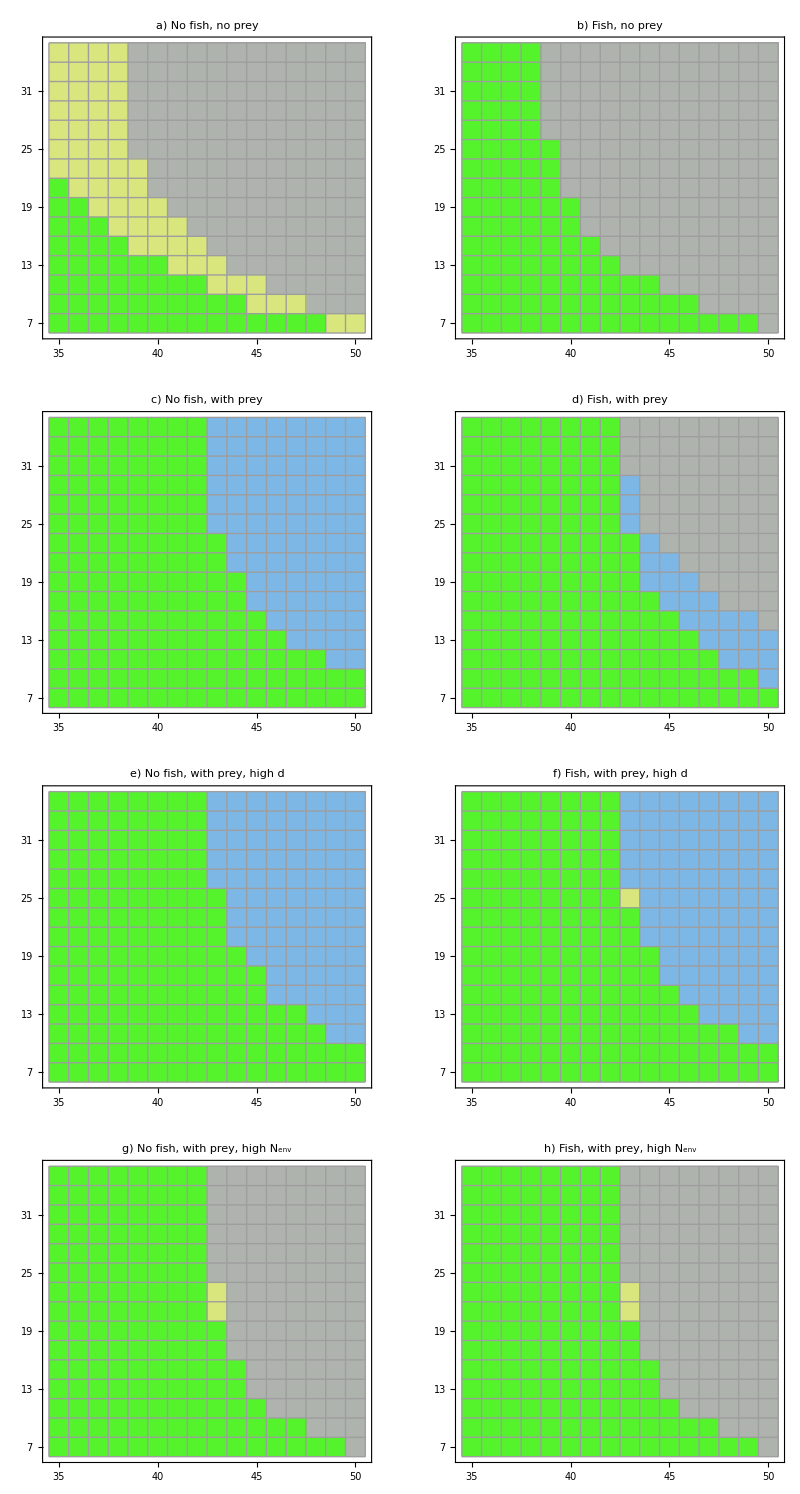
-Graphics-Light pulse duration (d)Light pulse magnitude (mol photons m^-2 d^-1)

```mathematica
(*make figure 5*)
heatmapFig=Legended[Labeled[GraphicsGrid[{{plot5a, plot5b}, {plot5c, plot5d}, {plot5e, plot5f}, {plot5g, plot5h}}, ImageSize->Full,Spacings->{ {0(*left to right*)},{0,10,10,10(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],{"Light pulse duration (d)","Light pulse magnitude (mol photons m^-2 d^-1)"},{Left,Bottom},RotateLabel->True,LabelStyle->Directive[FontColor-> Black, FontFamily-> "Helvetica", 16]],Placed[heatmapLeg,(*Bottom*){1.5,0.8(*x, y position of the legend*)}]]
```

```mathematica
Export["heatmaps_fig.pdf",heatmapFig,"PDF"]
```

heatmaps_fig.pdf

## Code to produce Figure 6 (Effects of varying environmental conditions on recovery from bleaching)

### Check to make sure the system bleached in all cases

```mathematica
(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=35;

(*use Manipulate to vary the parameters over the ranges simulated below and make sure bleaching occurs in all cases*)
Manipulate[
Module[{jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t},
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG;

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};
(*get all state variables*)
states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); (* this is changing all the state variables from X to X[t] instead of writing X[t] everywhere*)
(*put together equations (with ODE method)*)
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars)
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];
sol=NDSolve[Join[eqs,inis],#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];
(* results to plot*)
Multicolumn[{
Plot[Evaluate[H'[t]/H[t]/.sol], {t,0,tmax},PlotRange->Full,AxesLabel->{"t"},PlotLabel->"dH/Hdt",ImageSize->Medium,AxesOrigin->{0,0}],
Plot[{Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol}},{t,0,tmax},PlotLabel->"H SU Limitation",PlotRange->Full,AxesLabel->{"t"},ImageSize->Medium,AxesOrigin->{0,0}],
Plot[{Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol}},{t,0,tmax},PlotLabel->"S SU Limitation",PlotRange->Full,AxesLabel->{"t"},ImageSize->Medium,AxesOrigin->{0,0}],
Plot[Evaluate[S[t]/H[t]/.sol], {t,0,tmax},PlotRange->Full,AxesLabel->{"t"},PlotLabel->"S/H",ImageSize->Medium,AxesOrigin->{0,0}],Plot[Evaluate[S'[t]/S[t]/.sol], {t,0,tmax},PlotRange->Full,AxesLabel->{"t"},PlotLabel->"dS/Sdt",ImageSize->Medium,AxesOrigin->{0,0}],
Plot[{Evaluate[Ni[t]/.sol], Ν}, {t,0,tmax},PlotRange->Full,AxesLabel->{"t"},PlotLabel->"Ni",ImageSize->Medium,AxesOrigin->{0,0}]
}, 2]],
{{tHigh,30}, 0,42},
{{LHigh,35}, 0, 36},
{{kp,210}, 17, 359},
{{ep,1.5*10^-5}, 1.63*10^-6, 0.001},
{{P0,0}, 0, kp*(1-α)*H0},
{{X,0}, 0, 10^-6},
{{Ν,1*10^-7}, 10^-8, 4*10^-6},
{{L,15},10, 50},
{{d, 1660}, 443, 2880},
{{rp, 0.05}, 0.05, 1},
{{tmax,1000}, 100, 5000},
ContinuousAction->False
]
```

For tHigh=30 and LHigh=35, still get bleaching at max prey (2*10^-7) and at highest prey and highest flushing rate (d=4000), so this seems ok to use
Also tmax=1000 seems to be long enough to let return to positive growth happen even in the “worst” cases (no prey, low flushing rate, highest fish carrying capacity)

prey=1.1*10^-7, no fish: for Nenv greater than or equal to 3.7*10^-7, no recovery (stabilizes in bleached state), same with fish... how to show this on plot? Just don’t go this high and mention recovery does not happen for greater N? for 3.6*10^-7 or less, tmax=1200 should be long enough to capture recovery

### Simulations varying prey

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=1000; 

(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=35;

XRecovRuns= Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,HGrowthVals, PosGrowth,HSULim,HNLim,SSULim,SNLim,RecoveryTime(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t,  H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*host growth values*)
(*all host growth values from the end of stress*)
HGrowthVals=Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tStartStress+tHigh+1,tmax}]];
(* position of these values at which growth is positive, which corresponds to the number of days after stress: if 1st position is pos., then growth was pos. 1 day after stress ended, etc. *)
PosGrowth=Flatten[Position[HGrowthVals,_?(#> 0&)]][[1]]; 

(*host biomass SU limitation from end of stress*)
HSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
(*position at which these values become positive (meaning the SU is N limited)*)
HNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(*symbiont biomass SU limitation from end of stress*)
SSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
(*position at which these values become positive (meaning the SU is N limited)*)
SNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(* time to recovery= when H growth is pos and both H and S SU are back at N-lim, so take the maximum of the positions at which these occur*)
RecoveryTime=Max[PosGrowth, HNLim, SNLim];


{RecoveryTime}(*record time to recovery*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{X,{0,0.1*10^-7,0.2*10^-7,0.3*10^-7,0.4*10^-7,0.5*10^-7,0.6*10^-7,0.7*10^-7,0.8*10^-7,0.9*10^-7,1*10^-7,1.1*10^-7,1.2*10^-7,1.3*10^-7,1.4*10^-7,1.5*10^-7,1.6*10^-7,1.7*10^-7,1.8*10^-7,1.9*10^-7, 2*10^-7}}(*different levels of prey*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["XRecov",XRecovRuns];
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["XRecov"];
```

#### Get the results in the correct form to plot

```mathematica
(*getting the lists to plot (have 2 (fish/no fish) for each of the 3 outputs, so 6 lists total*)
(*transpose this to change the nested list from {{P1 at X1, P2 at X1}, {X2}, ...{Xn}} to {{X1, X2, ... Xn at P1}, {P2}} *)
XRecovSeparatePX=Transpose[XRecovRuns];
(*prey no fish*)
XRecovNoPX=Flatten[XRecovSeparatePX[[1]]];
(*with prey with fish*)
XRecovPX=Flatten[XRecovSeparatePX[[2]]];

(*list of X values*)
XVals2={0,0.1*10^-7,0.2*10^-7,0.3*10^-7,0.4*10^-7,0.5*10^-7,0.6*10^-7,0.7*10^-7,0.8*10^-7,0.9*10^-7,1*10^-7,1.1*10^-7,1.2*10^-7,1.3*10^-7,1.4*10^-7,1.5*10^-7,1.6*10^-7,1.7*10^-7,1.8*10^-7,1.9*10^-7, 2*10^-7};

(*use Table to get the lists in the form to plot*)
XRecovLists=Table[Module[{PlotList},PlotList=Transpose@{XVals2,list}; PlotList], {list, {XRecovNoPX,XRecovPX}}];
```

### Simulations varying flushing rate

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

X=1.1*10^-7;(*prey level*)

(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=35;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=1000; 

dRecovRuns=
Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,HGrowthVals, PosGrowth,HSULim,HNLim,SSULim,SNLim,RecoveryTime(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*host growth values*)
(*all host growth values from the end of stress*)
HGrowthVals=Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tStartStress+tHigh+1,tmax}]];
(* position of these values at which growth is positive, which corresponds to the number of days after stress at which positive growth is reached *)
PosGrowth=Flatten[Position[HGrowthVals,_?(#> 0&)]][[1]]; 

(*host biomass SU limitation*)
HSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
HNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(*symbiont biomass SU limitation*)
SSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
SNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(* time to recovery= when H growth is pos and both H and S SU are back at N-lim, so take the maximum of the positions at which these occur*)
RecoveryTime=Max[PosGrowth, HNLim, SNLim];

{RecoveryTime}(*the steady state values as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{d,{450,650,850,1050,1250,1450,1650,1850,2050,2250,2450,2650,2850,3050,3250,3450,3650,3850,4050}}(*repeat all this for different flushing rates*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["dRecov",dRecovRuns];
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["dRecov"];
```

#### Get the results in the correct form to plot

```mathematica
(*transpose this to change the nested list from {{P1 at d1, P2 at d1}, {d2}, ...{dn}} to {{d1, d2, ... dn at P1}, {P2}} *)
dRecovSeparatePX=Transpose[dRecovRuns];
(*prey no fish*)
dRecovNoPX=Flatten[dRecovSeparatePX[[1]]];
(*with prey with fish*)
dRecovPX=Flatten[dRecovSeparatePX[[2]]];

(*list of flushing rate values*)
dVals2={450,650,850,1050,1250,1450,1650,1850,2050,2250,2450,2650,2850,3050,3250,3450,3650,3850,4050};

(*use Table to get the lists in the form to plot*)
dRecovLists=Table[Module[{PlotList},PlotList=Transpose@{dVals2,list}; PlotList], {list, {dRecovNoPX,dRecovPX}}];
```

### Simulations varying fish carrying capacity

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(*environmental parameters*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

X=1.1*10^-7;

jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);

tmax=1000; 

(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=35;

kpRecovRuns=
Table[
Table[
Module[{

jX=(jXm X)/(X+KX),(* jN=(jNm Ν)/(Ν+KN),*)jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0,(* Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),*)states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,HGrowthVals, PosGrowth,HSULim,HNLim,SSULim,SNLim,RecoveryTime(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];

F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P01*kp*(1-α)*H0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*host growth values*)
(*all host growth values from the end of stress*)
HGrowthVals=Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tStartStress+tHigh+1,tmax}]];
(* position of these values at which growth is positive, which corresponds to the number of days after stress at which the host returns to positive growth*)
PosGrowth=Flatten[Position[HGrowthVals,_?(#> 0&)]][[1]]; 

(*host biomass SU limitation*)
HSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
HNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(*symbiont biomass SU limitation*)
SSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
SNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(* time to recovery= when H growth is pos and both H and S SU are back at N-lim, so take the maximum of the positions at which these occur*)
RecoveryTime=Max[PosGrowth, HNLim, SNLim];

{RecoveryTime}(*the steady state values as output*)],

{P01, {0, 1}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0) but since kp is changing, use a dummy variable P01 in order to have kp only chnge within Table and not also in the values to iterate over*)
{kp,{1, 25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400}}(*repeat all this for different kps*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["kpRecov",kpRecovRuns];
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["kpRecov"];
```

#### Get the results in the correct form to plot

```mathematica
(*transpose this to change the nested list from {{P1 at kp1, P2 at kp1}, {kp2}, ...{kpn}} to {{kp1, kp2, ... kpn at P1}, {P2}} *)
kpRecovSeparatePX=Transpose[kpRecovRuns];
(*prey no fish*)
kpRecovNoPX=Flatten[kpRecovSeparatePX[[1]]];
(*with prey with fish*)
kpRecovPX=Flatten[kpRecovSeparatePX[[2]]];

(*list of kp values*)
kpVals2={1, 25,50,75,100,125,150,175,200,225,250,275,300,325,350,375,400};

(*use Table to get the lists in the form to plot*)
kpRecovLists=Table[Module[{PlotList},PlotList=Transpose@{kpVals2,list}; PlotList], {list, {kpRecovNoPX,kpRecovPX}}];
```

### Simulations varying Nenv

#### Run the simulations

```mathematica
(*clear parameters that are changing and intermediate values*)
ClearAll[X, P0,jX,Ν,jN,Ni0,jNi0,jHG, jSG,ρN,jeC,jCO2,jL,rCH,rCS,jeL,jNPQ,cROS1,jST,rNH,A,jNw, tsolve, states, eqs, inis, sol,t,tmax, tHigh, LHigh,LfunH]
```

```mathematica
(* environment: flushing rate and N level*)
d=1660;
Ν=1*10^-7 (*1*10^-6*);

X=1.1*10^-7;(*prey level*)

(*light function values*)
tStartStress=600;
tHigh=30;
LHigh=35;

(*jN=(jNm Ν)/(Ν+KN); 
Ni0 = Ν;
jNi0 = (jNm Ν)/(Ν+KN);*)

tmax=1200; 


NRecovRuns=
Table[
Table[
Module[{

jX=(jXm X)/(X+KX), jN=(jNm Ν)/(Ν+KN),jHT=j0HT,rNS=σNS nNS j0ST,VH0=kv*H0, Ni0 = Ν,jNi0 = (jNm Ν)/(Ν+KN),states, rNH, S,H,VH,P,Ni,jNi,ρC, jCP, jHG,ρN,jeC,jCO2,A,jL,rCH,rCS,jeL,jNPQ,cROS1,jSG,jST,jNw,F,fh,LfunH,tsolve, addtimetostatevars,eqs,inis,sol,t,HGrowthVals, PosGrowth,HSULim,HNLim,SSULim,SNLim,RecoveryTime(*make sure to put any intermediate output values in Module*)},
(*light function*)
LfunH=L+ LHigh*HeavisideTheta[t-tStartStress] -  LHigh*HeavisideTheta[t-(tStartStress+tHigh)];
F[ρ_][A_,B_]:=(A B (A+B) ρ)/(A^2 B+A B^2+A^2 ρ+A B ρ+B^2 ρ);(*same as 1/(1/ρ+1/A+1/B-1/(A+B))*)
(* helper function for VH*)
fh[t_?NumericQ,y_]:=Piecewise[{{0, y<0},{kv *y,y≥0}}];

(* Calculations *)
jHG=F[jHGm][yC (ρC S/H+jX),((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]; 
jSG=F[jSGm][jCP yC,(rNS+(H ρN)/S)/nNS];
ρN=Max[(1-α)*jNi+α*jN+nNX jX+rNH-nNH jHG ,0];
jeC=Max[jX-jHG/yC+(S ρC)/H,0]; 
jCO2=jeC kCO2;
jL=A astar LfunH ;
rCH=(jHT+(jHG (1-yC))/yC) σCH;
rCS=σCS(j0ST+(1-yC)jSG yC^-1);
jeL=jL-jCP/yCL;
jNPQ=1/(1/jeL+1/kNPQ);
cROS1=(jeL-jNPQ)/kROS;
jST=(1+b cROS1) j0ST;
rNH=σNH nNH jHT;
A=1.256307+1.385969 ⅇ^(-6.479055 S/H);
jNw= ρN*H/S+rNS-nNS*jSG; 

tsolve={
{ρC,jCP-jSG yC^-1,ρC0},
{jCP,(F[jCPm][jL yCL,rCS+(H (jCO2+rCH))/S])/(1+cROS1),jCP0},
{jNi, (jNm *Ni)/(Ni+KN), jNi0}
};

states=Join[tsolve[[All,1]],{H,S,VH, Ni,P}];
addtimetostatevars=((#->#[t])&/@states); 
eqs=Join[
(#[[1]]'[t]==(λ(Max[0,#[[2]]]-#[[1]])/.addtimetostatevars))&/@tsolve,
{
S'[t]==(S(jSG-jST)/.addtimetostatevars),
H'[t]==(H(jHG-jHT)/.addtimetostatevars),
VH'[t]== fh[t, H'[t]],
Ni'[t]== (d*( Ν - Ni) +(ζ*(1-α)*jNw*S+ ep*P -jNi*(1-α)*H)/( vi*VH)/.addtimetostatevars),
P'[t] == (P*(rp*(kp*(1-α)H-Bp*P)/(kp*(1-α)H))/.addtimetostatevars) 
}
];
(*set initial conditions*)
inis=Join[{
H[0]==H0,
S[0]==S0,
VH[0]==VH0,
Ni[0]== Ni0,
P[0]==P0},
(#[[1]][0]==#[[3]])&/@tsolve];

sol=NDSolve[{Join[eqs,inis]},#&/@states,{t,0,tmax},Method->{"EquationSimplification"->"Residual"}][[1]];

(*host growth values*)
(*all host growth values from the end of stress*)
HGrowthVals=Flatten[Table[Evaluate[{H'[t]/H[t]}/.sol],{t,tStartStress+tHigh+1,tmax}]];
(* position of these values at which growth is positive, which corresponds to the number of days after stress at which the host returns to positive growth*)
PosGrowth=Flatten[Position[HGrowthVals,_?(#> 0&)]][[1]]; 

(*host biomass SU limitation*)
HSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jHGm,yC (ρC S/H+jX)]/Min[jHGm,((1-α)*jNi+α*jN+nNX jX+rNH)nNH^-1]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
HNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(*symbiont biomass SU limitation*)
SSULim=Flatten[Table[Evaluate@Flatten@{Log[Min[jSGm,jCP yC]/Min[jSGm,(rNS+(H ρN)/S)/nNS]]/.addtimetostatevars/.sol},{t,tStartStress+tHigh+1,tmax}]];
SNLim=Flatten[Position[HSULim,_?(#> 0&)]][[1]]; 

(* time to recovery= when H growth is pos and both H and S SU are back at N-lim, so take the maximum of the positions at which these occur*)
RecoveryTime=Max[PosGrowth, HNLim, SNLim];

{RecoveryTime}(*the steady state values as output*)],

{P0, {0, kp*(1-α)*H0}}],(*iterate the above once with no fish (P0=0) and once with fish (P0=kp*(1-α)*H0)*)
{Ν,{0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7,2*10^-7,2.25*10^-7,2.5*10^-7,2.75*10^-7,3*10^-7,3.25*10^-7,3.5*10^-7}}(*repeat all this for different Nenv*)
];
```

```mathematica
(*storing these simulations so Mathematica saves them when this notebook is closed*)
Save["NRecov",NRecovRuns];
```

```mathematica
(*reload the runs: need to do this each time this notebook gets re-opened*)
Get["NRecov"];
```

#### Get the results in the correct form to plot

```mathematica
(*transpose this to change the nested list from {{P1 at N1, P2 at N1}, {N2}, ...{Nn}} to {{N1, N2, ... Nn at P1}, {P2}} *)
NRecovSeparatePX=Transpose[NRecovRuns];
(*prey no fish*)
NRecovNoPX=Flatten[NRecovSeparatePX[[1]]];
(*with prey with fish*)
NRecovPX=Flatten[NRecovSeparatePX[[2]]];

(*list of Nenv values*)
NVals2={0.1*10^-7,0.25*10^-7,0.5*10^-7,0.75*10^-7,1*10^-7,1.25*10^-7,1.5*10^-7,1.75*10^-7,2*10^-7,2.25*10^-7,2.5*10^-7,2.75*10^-7,3*10^-7,3.25*10^-7,3.5*10^-7};

(*use Table to get the lists in the form to plot*)
NRecovLists=Table[Module[{PlotList},PlotList=Transpose@{NVals2,list}; PlotList], {list, {NRecovNoPX,NRecovPX}}];
```

### Make Figure 6

```mathematica
(*padding for the plots*)
padding6={{50(*left*),15(*right*)}, {45(*bottom*),10 (*top*)}};

(*results of prey simulations*)
plot6a=ListLinePlot[{XRecovLists[[1]], XRecovLists[[2]]},PlotLabel->"a) Effect of prey on recovery",PlotRange->{Full, {0, 350}},ImageSize->Full,ImagePadding->padding6,LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{100}}, GridLinesStyle->Directive[Black, Dashed],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Time in bleached state (d)",None},{"Prey (C-mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)];

(*results of Nenv simulations*)
plot6b= ListLinePlot[{NRecovLists[[1]], NRecovLists[[2]]},PlotLabel->"b) Effect of ambient nitrogen on recovery",LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->{Full, {0, 350}},ImageSize->Full,ImagePadding->padding6,PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{100}}, GridLinesStyle->Directive[Black, Dashed],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None},{"Ambient N (mol L^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)];

(*results of flushing rate simulations*)
plot6c= ListLinePlot[{dRecovLists[[1]], dRecovLists[[2]]},PlotLabel->"c) Effect of flushing rate on recovery",LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->{Full, {0, 130}},ImageSize->Full,ImagePadding->padding6,PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{100}}, GridLinesStyle->Directive[Black, Dashed],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{"Time in bleached state (d)",None},{"Flushing rate (d^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)];

(*results of kp simulations*)
plot6d= ListLinePlot[{kpRecovLists[[1]], kpRecovLists[[2]]},PlotLabel->"d) Effect of fish abundance on recovery",LabelStyle-> Directive[FontColor-> Black, FontFamily-> "Helvetica", 12(*label size*)],PlotRange->{Full, {0, 130}},ImageSize->Full,ImagePadding->padding6,PlotStyle->{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]},GridLines->{{},{100}}, GridLinesStyle->Directive[Black, Dashed],Frame->{{True(*left*), False(*right*)},{True(*bottom*),False(*top*)}}, (*FrameTicks->(*True*){{{0, 0.01,0.02,0.03,0.04,0.05},None},{(*None*){{0, "0"},{2*10^-7, "0.2"},{4*10^-7, "0.4"},{6*10^-7, "0.6"},{8*10^-7, "0.8"},{1*10^-6, "1.0"}},None}},*)FrameLabel->{{None,None},{"Fish:host biomass scalar (g fish C-mol H^-1)",None}}, FrameTicksStyle->Directive[Black,10(*size of ticks*)], FrameStyle->Directive[Black,12](*axis label size*)];
```

```mathematica
(*make the legend*)
RecovLeg=LineLegend[{ColorData[97,"ColorList"][[1]], ColorData[97,"ColorList"][[2]]}, {"Fish absent","Fish present"}, LegendMarkerSize->40(*, LegendLayout->{"Row",1}*)]
```

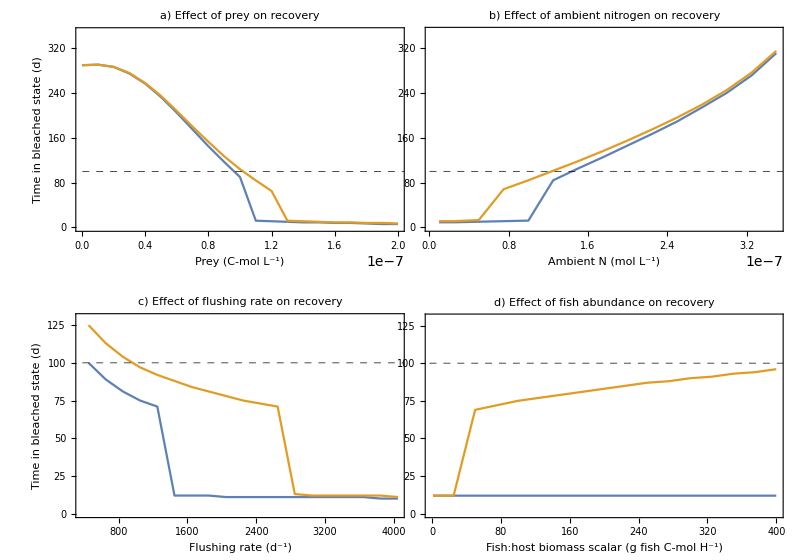

```mathematica
(*make figure 6*)
RecovFig=Show[Legended[GraphicsGrid[{{plot6a, plot6b}, {plot6c, plot6d}}, ImageSize->Full,Spacings->{ {0(*left*),-100 (*first (leftmost) and second col*)(*left to right*)},{0(*top*),30(*first and second rows*)(*top to bottom*)}}, Frame->False(*, AspectRatio->1/GoldenRatio*), Alignment-> Bottom],Placed[RecovLeg,(*Bottom*){1.4, 0.70(*x, y position of legend*)}]], Graphics[{Text["Mortality",{260 (*more pos=farther right*),-375(*more neg=further down*)}],Text["Recovery",{260 (*more pos=farther right*),-435(*more neg=further down*)}]}]]
```